```mathematica
path = FileNameJoin[{NotebookDirectory[],"generations.csv"}];
```

```mathematica
data=Import[path];
```

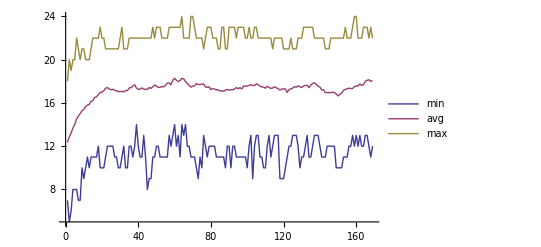

```mathematica
ListLinePlot[Transpose[data],PlotLegends-> {"min", "avg","max"}]
```

```mathematica
Export["plot.png",%];
```